# The expected SFS under positive selection Here I examine the expected uSFS under positive selection, based on results from Poisson Random Field theory.

### Neutral SFS Let’s start by examining the SFS expected under neutrality...

```mathematica
NeutSFS[THETA_,i_ ]:=THETA/i
```

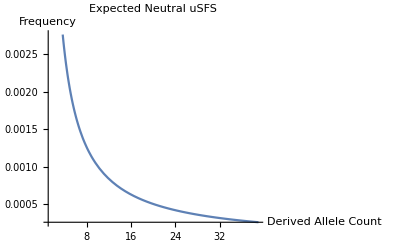

and classic Hartl is of PRF reusult Sawyer the This...

```mathematica
Plot[NeutSFS[0.01,i], {i,1,39},AxesLabel->{"Derived Allele Count","Frequency"},PlotLabel->"Expected Neutral uSFS"]

This is the classic PRF reusult of Sawyer and Hartl...
```

### SFS for positively selected mutations Now let’s look at the uSFS expected under strong positive selection...

```mathematica
SelSFSfixed[S_,pA_,THETA_,i_, n_]:=Module[{H,B},
H[x_] = (1 - Exp[-S*(1-x)]) / (x*(1-x)*(1-Exp[-S]));
B[x_] = Binomial[n,i] * (x^i)*(1-x)^(n-i);
THETA*pA*NIntegrate[B[i,n,x]*H[x],{x,0,1}]]
```

```mathematica
Plot[SelSFSfixed[1000,0.01,i,40], {i,1,39},AxesLabel->{"Derived Allele Count","Frequency"},PlotLabel->"Expected Neutral uSFS"]
```

-Graphics-

```mathematica
SelSFSpoint[S_,pA_,THETA_,i_, n_]:=Module[{H,B},
H[x_] = (1 - Exp[-S*(1-x)]) / (x*(1-x)*(1-Exp[-S]));
B[x_] = Binomial[n,i] * (x^i)*(1-x)^(n-i);
THETA*NIntegrate[B[i,n,x]*H[x],{x,0.001,0.999}]]
```

```mathematica
SelSFSpoint[100,0.001,0.01,1,40]
```

NIntegrate::inumr: The integrand ((1-ⅇ^(-100 (1-x))) B$128408[1,40,x])/((1-1/ⅇ^100) (1-x) x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.001,0.999}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.01 NIntegrate[B$128408[1,40,x] H$128408[x],{x,0.001,0.999}]

```mathematica
H[S_,x_] = (1 - Exp[-S*(1-x)]) / (x*(1-x)*(1-Exp[-S]));

B[i_,n_,x_] = Binomial[n,i] * (x^i)*(1-x)^(n-i);

0.01*0.001*Integrate[H[100,x]*B[3,40,x],{x,0,1}]
```

3.6036×10^-6

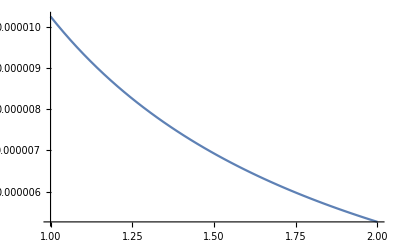

```mathematica
Plot[(0.01 *0.001* Integrate[H[1000,x]*B[i,40,x],{x,0,1}]),{i,1,2}]
```

```mathematica
SFS = Table[ { 100,0.001,i, 0.01*0.001*Integrate[H[100,x]*B[i,40,x],{x,0,1}]},  {i, 1,2}] ;
```

```mathematica
SFS
```

{{100,0.001,1,0.0000102564},{100,0.001,2,5.26316×10^-6}}

```mathematica
headers={"S","pA","i","SFS_i"};

SFS1000pA0001 = Table[ { 1000,0.0001,i, 0.01*0.0001*NIntegrate[H[1000,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS500 = Table[ { 500,0.0001,i, 0.01*0.0001*NIntegrate[H[500,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS100 = Table[ { 100,0.001,i, 0.01*0.001*NIntegrate[H[100,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS10 = Table[ { 10,0.01,i, 0.01*0.01*NIntegrate[H[10,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;

data1000=Prepend[SFS1000,headers]
data500=Prepend[SFS500,headers]
data100=Prepend[SFS100,headers]
data10=Prepend[SFS10,headers]

Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS1000.csv",data1000];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS500.csv",data500];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS100.csv",data100];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS10.csv",data10];
```

{{S,pA,i,SFS_i},{1000,0.0001,1,1.02564×10^-6},{1000,0.0001,2,5.26316×10^-7},{1000,0.0001,3,3.6036×10^-7},{1000,0.0001,4,2.77778×10^-7},{1000,0.0001,5,2.28571×10^-7},{1000,0.0001,6,1.96078×10^-7},{1000,0.0001,7,1.7316×10^-7},{1000,0.0001,8,1.5625×10^-7},{1000,0.0001,9,1.43369×10^-7},{1000,0.0001,10,1.33333×10^-7},{1000,0.0001,11,1.25392×10^-7},{1000,0.0001,12,1.19048×10^-7},{1000,0.0001,13,1.1396×10^-7},{1000,0.0001,14,1.0989×10^-7},{1000,0.0001,15,1.06667×10^-7},{1000,0.0001,16,1.04167×10^-7},{1000,0.0001,17,1.02302×10^-7},{1000,0.0001,18,1.0101×10^-7},{1000,0.0001,19,1.00251×10^-7},{1000,0.0001,20,1.×10^-7},{1000,0.0001,21,1.00251×10^-7},{1000,0.0001,22,1.0101×10^-7},{1000,0.0001,23,1.02302×10^-7},{1000,0.0001,24,1.04167×10^-7},{1000,0.0001,25,1.06667×10^-7},{1000,0.0001,26,1.0989×10^-7},{1000,0.0001,27,1.1396×10^-7},{1000,0.0001,28,1.19048×10^-7},{1000,0.0001,29,1.25392×10^-7},{1000,0.0001,30,1.33333×10^-7},{1000,0.0001,31,1.43369×10^-7},{1000,0.0001,32,1.5625×10^-7},{1000,0.0001,33,1.7316×10^-7},{1000,0.0001,34,1.96078×10^-7},{1000,0.0001,35,2.28571×10^-7},{1000,0.0001,36,2.77777×10^-7},{1000,0.0001,37,3.60343×10^-7},{1000,0.0001,38,5.25591×10^-7},{1000,0.0001,39,9.87107×10^-7}}

{{S,pA,i,SFS_i},{500,0.0001,1,1.02564×10^-6},{500,0.0001,2,5.26316×10^-7},{500,0.0001,3,3.6036×10^-7},{500,0.0001,4,2.77778×10^-7},{500,0.0001,5,2.28571×10^-7},{500,0.0001,6,1.96078×10^-7},{500,0.0001,7,1.7316×10^-7},{500,0.0001,8,1.5625×10^-7},{500,0.0001,9,1.43369×10^-7},{500,0.0001,10,1.33333×10^-7},{500,0.0001,11,1.25392×10^-7},{500,0.0001,12,1.19048×10^-7},{500,0.0001,13,1.1396×10^-7},{500,0.0001,14,1.0989×10^-7},{500,0.0001,15,1.06667×10^-7},{500,0.0001,16,1.04167×10^-7},{500,0.0001,17,1.02302×10^-7},{500,0.0001,18,1.0101×10^-7},{500,0.0001,19,1.00251×10^-7},{500,0.0001,20,1.×10^-7},{500,0.0001,21,1.00251×10^-7},{500,0.0001,22,1.0101×10^-7},{500,0.0001,23,1.02302×10^-7},{500,0.0001,24,1.04167×10^-7},{500,0.0001,25,1.06667×10^-7},{500,0.0001,26,1.0989×10^-7},{500,0.0001,27,1.1396×10^-7},{500,0.0001,28,1.19048×10^-7},{500,0.0001,29,1.25392×10^-7},{500,0.0001,30,1.33333×10^-7},{500,0.0001,31,1.43369×10^-7},{500,0.0001,32,1.5625×10^-7},{500,0.0001,33,1.7316×10^-7},{500,0.0001,34,1.96078×10^-7},{500,0.0001,35,2.28571×10^-7},{500,0.0001,36,2.77771×10^-7},{500,0.0001,37,3.60232×10^-7},{500,0.0001,38,5.23612×10^-7},{500,0.0001,39,9.51301×10^-7}}

{{S,pA,i,SFS_i},{100,0.001,1,0.0000102564},{100,0.001,2,5.26316×10^-6},{100,0.001,3,3.6036×10^-6},{100,0.001,4,2.77778×10^-6},{100,0.001,5,2.28571×10^-6},{100,0.001,6,1.96078×10^-6},{100,0.001,7,1.7316×10^-6},{100,0.001,8,1.5625×10^-6},{100,0.001,9,1.43369×10^-6},{100,0.001,10,1.33333×10^-6},{100,0.001,11,1.25392×10^-6},{100,0.001,12,1.19048×10^-6},{100,0.001,13,1.1396×10^-6},{100,0.001,14,1.0989×10^-6},{100,0.001,15,1.06667×10^-6},{100,0.001,16,1.04167×10^-6},{100,0.001,17,1.02302×10^-6},{100,0.001,18,1.0101×10^-6},{100,0.001,19,1.00251×10^-6},{100,0.001,20,1.×10^-6},{100,0.001,21,1.00251×10^-6},{100,0.001,22,1.0101×10^-6},{100,0.001,23,1.02302×10^-6},{100,0.001,24,1.04167×10^-6},{100,0.001,25,1.06667×10^-6},{100,0.001,26,1.0989×10^-6},{100,0.001,27,1.1396×10^-6},{100,0.001,28,1.19048×10^-6},{100,0.001,29,1.25392×10^-6},{100,0.001,30,1.33333×10^-6},{100,0.001,31,1.43368×10^-6},{100,0.001,32,1.56246×10^-6},{100,0.001,33,1.73142×10^-6},{100,0.001,34,1.95998×10^-6},{100,0.001,35,2.28216×10^-6},{100,0.001,36,2.76159×10^-6},{100,0.001,37,3.52598×10^-6},{100,0.001,38,4.85006×10^-6},{100,0.001,39,7.36369×10^-6}}

{{S,pA,i,SFS_i},{10,0.01,1,0.000102563},{10,0.01,2,0.0000526298},{10,0.01,3,0.0000360339},{10,0.01,4,0.0000277752},{10,0.01,5,0.000022854},{10,0.01,6,0.000019604},{10,0.01,7,0.0000173113},{10,0.01,8,0.0000156192},{10,0.01,9,0.0000143298},{10,0.01,10,0.0000133245},{10,0.01,11,0.0000125282},{10,0.01,12,0.0000118911},{10,0.01,13,0.0000113788},{10,0.01,14,0.0000109674},{10,0.01,15,0.0000106395},{10,0.01,16,0.0000103823},{10,0.01,17,0.0000101866},{10,0.01,18,0.0000100455},{10,0.01,19,9.95419×10^-6},{10,0.01,20,9.90925×10^-6},{10,0.01,21,9.90847×10^-6},{10,0.01,22,9.95072×10^-6},{10,0.01,23,0.0000100358},{10,0.01,24,0.0000101642},{10,0.01,25,0.0000103374},{10,0.01,26,0.0000105577},{10,0.01,27,0.0000108279},{10,0.01,28,0.000011152},{10,0.01,29,0.0000115349},{10,0.01,30,0.0000119823},{10,0.01,31,0.0000125012},{10,0.01,32,0.0000130999},{10,0.01,33,0.0000137882},{10,0.01,34,0.0000145775},{10,0.01,35,0.0000154812},{10,0.01,36,0.000016515},{10,0.01,37,0.0000176972},{10,0.01,38,0.0000190489},{10,0.01,39,0.0000205951}}

```mathematica
headers={"S","pA","i","SFS_i"};

SFS1000pA0001 = Table[ { 1000,0.0001,i, 0.01*0.0001*NIntegrate[H[1000,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS500pA0001 = Table[ { 500,0.0001,i, 0.01*0.0001*NIntegrate[H[500,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS100pA0001 = Table[ { 100,0.0001,i, 0.01*0.0001*NIntegrate[H[100,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS50pA0001 = Table[ { 50,0.0001,i, 0.01*0.0001*NIntegrate[H[50,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS10pA0001 = Table[ { 10,0.0001,i, 0.01*0.0001*NIntegrate[H[10,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;

SFS1000pA001 = Table[ { 1000,0.001,i, 0.01*0.001*NIntegrate[H[1000,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS500pA001 = Table[ { 500,0.001,i, 0.01*0.001*NIntegrate[H[500,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS100pA001 = Table[ { 100,0.001,i, 0.01*0.001*NIntegrate[H[100,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS50pA001 = Table[ { 50,0.001,i, 0.01*0.001*NIntegrate[H[50,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS10pA001 = Table[ { 10,0.001,i, 0.01*0.001*NIntegrate[H[10,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;

SFS1000pA01 = Table[ { 1000,0.01,i, 0.01*0.01*NIntegrate[H[1000,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS500pA01 = Table[ { 500,0.01,i, 0.01*0.01*NIntegrate[H[500,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS100pA01 = Table[ { 100,0.01,i, 0.01*0.01*NIntegrate[H[100,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS50pA01 = Table[ { 50,0.01,i, 0.01*0.01*NIntegrate[H[50,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;
SFS10pA01 = Table[ { 10,0.01,i, 0.01*0.01*NIntegrate[H[10,x]*B[i,40,x],{x,0,1}]},  {i, 1,39}] ;

data1000p01=Prepend[SFS1000pA01,headers]
data500p01=Prepend[SFS500pA01,headers]
data100p01=Prepend[SFS100pA01,headers]
data50p01=Prepend[SFS50pA01,headers]
data10p01=Prepend[SFS10pA01,headers]

data500=Prepend[SFS500,headers]
data100=Prepend[SFS100,headers]
data10=Prepend[SFS10,headers]

Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS1000.csv",data1000];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS500.csv",data500];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS100.csv",data100];Export["/Users/s0784966/UBC/uSFS_study/expected_uSFS/SFS10.csv",data10];
```